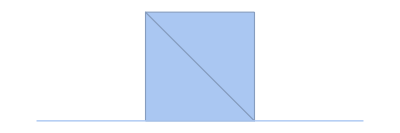

```mathematica
(*The shape we are solving over*)
newShape = MeshRegion[{{0,0},{1,0},{2,0},{3,0},{1,1},{2,1}},{Line[{1,4}],Simplex[{2,3,5}],Simplex[{3,5,6}]}]
```

```mathematica
(*The IC for the rod*)
ff[x_]:= -5*x*(x-3)
```

```mathematica
(*Solve the heat equation for the line first*)
alpha1 = 0.05; 
uvals = NDSolveValue[{{D[u[x,t],t]==alpha1*D[u[x,t],{x,2}]},{u[x,0]==ff[x]},{u[0,t]==0},{u[3,t]==0}},u,{x,0,3},{t,0,20}]
```

InterpolatingFunction[{{0., 3.}, {0., 20.}}, <>]

```mathematica
(*View the Heat of the Rod at different time points *)
Manipulate[Plot[{uvals[x,t],12},{x,0,3}],{t,0,20}]
```

```mathematica
(*Solve the heat equation for the square*)
```

```mathematica
alpha3 = 0.05;
vvals = NDSolveValue[{{D[v[x,y,t],t]==alpha3*(D[v[x,y,t],{x,2}]+D[v[x,y,t],{y,2}])},{v[x,y,0]==ff[x]},{v[x,0,t]==uvals[x,t]}},v,{x,1,2},{y,0,1},{t,0,20}]
```

NDSolveValue::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

NDSolveValue::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable y. Artificial boundary effects may be present in the solution.

InterpolatingFunction[{{1., 2.}, {0., 1.}, {0., 20.}}, <>]

```mathematica
(*View the heat of the square at different time points*)
```

```mathematica
Manipulate[Plot3D[{vvals[x,y,t],12},{x,1,2},{y,0,1}],{t,0,20}]
```